```mathematica
f[x_] := ArcTan[x]
g[x_] := Sqrt[1+x^2]
h=0.1;
α=1.5;
```

```mathematica
ϕ[s_,y_] := Exp[I s (y+f[y] h)] Exp[-h Abs[s g[y]]^α]
```

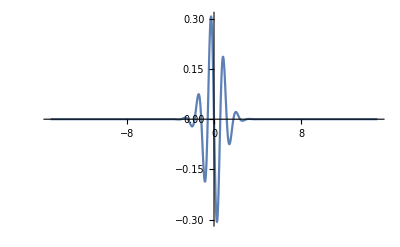

```mathematica
Plot[Im[ϕ[sgrid[[1]],y]],{y,-15,15},PlotRange->All]
```

```mathematica
Abs[ϕ[sgrid[[1]],-15]]
```

4.98621×10^-29

```mathematica
N[515/2]
```

257.5

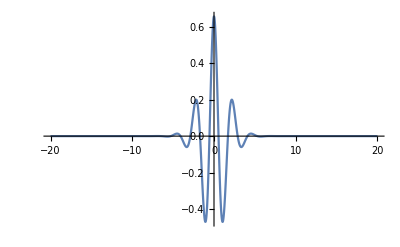

```mathematica
Plot[Re[ϕ[sgrid[[25]],y]],{y,-20,20},PlotRange->All]
```

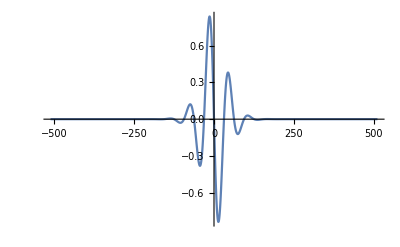

```mathematica
Plot[Im[ϕ[sgrid[[50]],y]],{y,-512,512},PlotRange->All]
```

```mathematica
Abs[ϕ[sgrid[[25]],-20]]
```

4.83522×10^-17

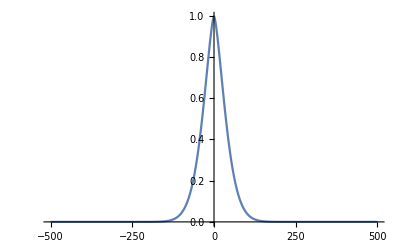

```mathematica
Plot[Abs[ϕ[sgrid[[50]],y]],{y,-500,500},PlotRange->All]
```

```mathematica
Abs[ϕ[sgrid[[50]],-500]]
```

4.41901×10^-16

```mathematica
c=0;
```

```mathematica
ψ0[s_] := Exp[I s c]
```

```mathematica
ss=0.1;
ssn=50;
sgrid=Table[n*ss,{n,-ssn,ssn}];
```

```mathematica
(* irange=Join[Table[i,{i,1,ssn}],Table[i,{i,ssn+2,2*ssn+1}]]; *)
```

```mathematica
kmat=ParallelTable[If[i==(ssn+1),If[i==j,1,0],NIntegrate[(1/(2 π)) ϕ[sgrid[[i]],y] Exp[-I sgrid[[j]] y],{y,-10,10}]],{i,1,2*ssn+1},{j,1,2*ssn+1}];
```

```mathematica
(* kmat[[51]]=Table[If[j==51,1,0],{j,1,2*ssn+1}] *)
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

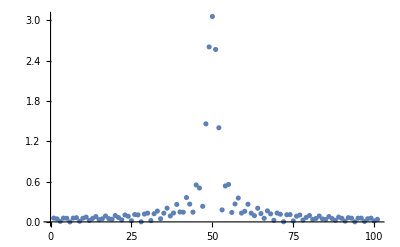

```mathematica
ListPlot[Abs[kmat[[50,;;]]],PlotRange->All]
```

```mathematica
ψ = Table[{ψ0[sgrid[[i]]]},{i,1,2*ssn+1}];
```

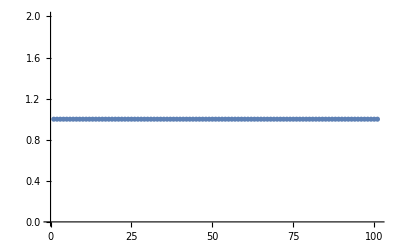

```mathematica
ListPlot[Flatten[ψ]]
```

```mathematica
For[i=1,i≤10,i++,ψ = kmat.ψ]
```

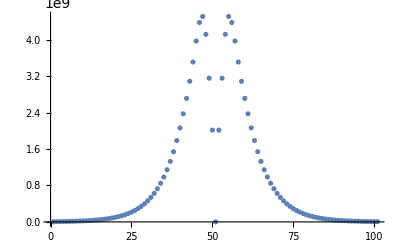

```mathematica
ListPlot[Abs[Flatten[ψ]],PlotRange->All]
```

```mathematica
Needs["FourierSeries`"]
```

```mathematica
kmat=ParallelTable[If[i==(ssn+1),If[i==j,1,0],NFourierTransform[ϕ[sgrid[[i]],y],y,sgrid[[j]]-sgrid[[i]],FourierParameters->{-1,-1}]],{i,1,2*ssn+1},{j,1,2*ssn+1}];
```

```mathematica
ListPlot[Abs[kmat[[42,;;]]],PlotRange->All]
```

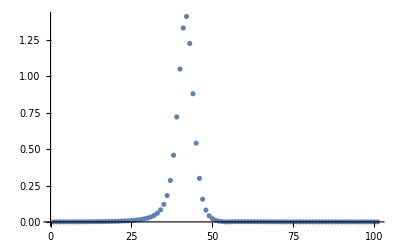

```mathematica
ψ = Table[{ψ0[sgrid[[i]]]},{i,1,2*ssn+1}];
```

```mathematica
For[i=1,i≤10,i++,ψ = kmat.ψ]
```

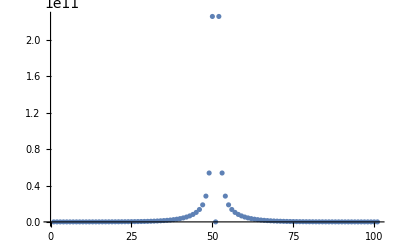

```mathematica
ListPlot[Abs[Flatten[ψ]],PlotRange->All]
```

```mathematica
(* my implementation of fractional Fourier transform *)
(* assume that x is a vector of length m *)
fracfft[x_,α_]:=Block[{m,y,z,yhat,zhat,temp},m=Length[x];
y = Join[x * Table[Exp[- π I j^2 α],{j,0,m-1}],Table[0,{j,0,m-1}]];
z = Join[Table[Exp[π I j^2 α],{j,0,m-1}],Table[Exp[π I (j - 2m)^2 α],{j,m,2*m-1}]];
yhat=Fourier[y,FourierParameters->{1,-1}];
zhat=Fourier[z,FourierParameters->{1,-1}];
temp=InverseFourier[yhat *zhat,FourierParameters->{1,-1}];
Table[Exp[-π I k^2 α],{k,0,m-1}]*temp[[1;;m]]]
```

```mathematica
fracfft[{1.3,-0.3},0.12]
```

{1.+0. ⅈ,1.08131+0.205364 ⅈ}

```mathematica
kmat1=ParallelTable[If[i==(ssn+1),If[i==j,1,0],
NIntegrate[(1/(2 π)) ϕ[sgrid[[i]],y] Exp[-I sgrid[[j]] y],{y,limits[[i]],-limits[[i]]}]],{i,1,ssn+1},{j,1,2*ssn+1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

```mathematica
kmat2=ParallelTable[If[i==(ssn+1),If[i==j,1,0],
NIntegrate[(1/(2 π)) ϕ[sgrid[[i]],y] Exp[-I sgrid[[j]] y],{y,limits[[2*ssn+2-i]],-limits[[2*ssn+2-i]]}]],{i,ssn+2,2*ssn+1},{j,1,2*ssn+1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

```mathematica
kmat=Join[kmat1,kmat2];
```

```mathematica
γ=0.01;
m=1024;
x[k_] := (k-m/2)γ
```

```mathematica
ygrid = Table[i,{i,-5000,5000}];
```

```mathematica
limits=Table[ygrid[[Ordering[Abs[Table[Abs[ϕ[x[i],y]],{y,ygrid}]- 1.2 10^(-16)],1][[1]]]],{i,0,m-1}];
```

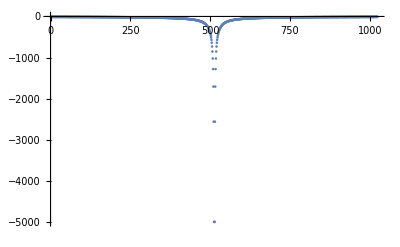

```mathematica
ListPlot[limits,PlotRange->All]
```

```mathematica
Abs[ϕ[x[511],-5000]]
```

4.41948×10^-16

```mathematica
-2*limits[[i]]
```

90

```mathematica
a
```

48

```mathematica
ϕ[x[i-1],t[0]]
```

-4.0109×10^-7+6.00003×10^-7 ⅈ

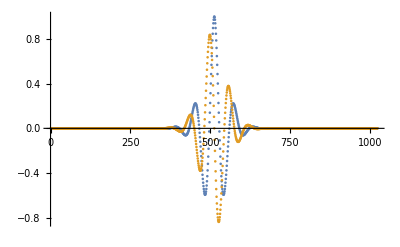

```mathematica
i=510;a=-2*limits[[i]];
(* put 1024 points in the interval no matter what *)
β=a/m;
t[j_] := (j-m/2)β
fvec=Table[ϕ[x[i-1],t[j]],{j,0,m-1}];
ListPlot[{Re[fvec],Im[fvec]},PlotRange->All]
```

```mathematica
δ=β γ/(2 π);
```

```mathematica
corrfac=Table[Exp[π I j m δ],{j,0,m-1}];
temp=β Table[Exp[π I (k-m/2)m δ],{k,0,m-1}]*fracfft[fvec*corrfac,δ];
```

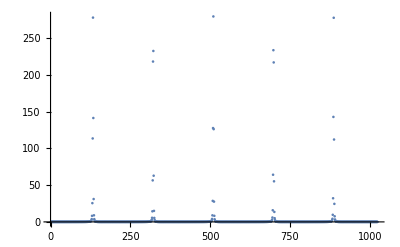

```mathematica
ListPlot[Abs[temp],PlotRange->All]
```